## Dodelson 7.2

## We attempt to compute the transfer function for a universe consisting of only radiation and dark matter. The transfer function, defined in Eqn. 7.3, is T[k] = (Φ[k,a_(late]))/Φ_ls[k,a_late].

```mathematica
<<Dodelson`ChangeVariable`
<<Dodelson`CommonParameters`
CommonDefinitions;
```

The definition of η : η'(t)→1/(a(η))  and define variables relative to equality point, a_eq, : y(η)→(a(η))/a_eq  and : y'(η)→(a'(η))/a_eq

The differential D[fn,η] in terms of change of variables to y is  fn'(η)→fn'(y) y'(η)

We have different forms of H : H→(a'(t))/(a(t))

And when using the definition y=a/a_eq   : H→(y'(η))/(a_eq (y(η))^2)

Scale factor at equality, a_eq -> a_eq→C_γ/(h^2 Ω_b)

Coefficient of radiation energy in terms of equality parameters -> C_γ→h^2 a_eq Ω_b

Other transformations referencing 'equality' point --> k_eq→√2 √((H_0^2 Ω_b)/a_eq)
and H_0→(√((a_eq k_eq^2)/Ω_b))/(√2)
and  k→k_eq kk_eq

Other relationships =>  R[a_eq] =  3/4

Sound speed -> √(1/(R_eq (3 ((R(a))/R_eq+1/R_eq)))) = 2/3 √(1/(4/3 (3 ρ_b(a))/(4 ρ_γ(a))+4/3)) =  2/3 √(1/(4/3 (3 ρ_b(a))/(4 ρ_γ(a))+4/3))

c_s[y=a/a_eq] = 2/3 √(1/(4/3 (3 ρ_b(y a_eq))/(4 ρ_γ(y a_eq))+4/3))

Find η[a] from H=a'/a=(8πGρ/3)^(1/2) -->

η[a] = (2 (√(h^2 (a+a_eq) Ω_b)-h √a_eq √Ω_b))/(h H_0 Ω_b)

Find  η[y = a/a_eq] =>

η_y[y = a/a_eq] = (2 (√(y+1)-1) √a_eq)/(H_0 √Ω_b)

Jacobian dη/dy for transforming integrals to integrals from dη to dy -> (√a_eq)/(√(y+1) H_0 √Ω_b)
Or  -> dη/dy = (√2)/(√(y+1) k_eq)

Find y[η] ->

y[η] = (η^2 Ω_b H_0^2+4 η √a_eq √Ω_b H_0)/(4 a_eq) = 1/8 η k_eq (η k_eq+4 √2)

Recombination definition of => z_*=1000 = 1000 ; a_*=1/(z_*+1) = 1/1001 ; y_*=(a_*)/a_eq = 1/(1001 a_eq)

Define Eqn.7.11-.11 and some simplications.

```mathematica
DefEqn711t15;
PrintEqn711t15;
sub=Solve[e711,Subscript[Θ, 1][η]]⟦1,1⟧;
e712a=Simplify[e712/.D[sub, η]];
e714a=FullSimplify[e714/.v'[η]->ⅈ vi'[η]/.v[η]->ⅈ vi[η]];
tmp=FullSimplify[%/.{a'[η]->Subscript[a, eq] y'[η],a[η]->Subscript[a, eq] y[η]}];
e714c=Simplify[Expand[(y[η] #1&)/@tmp]];
e713a=e713/.v[η]->ⅈ vi[η];
e715A=e715/.{Subscript[ρ, γ]->Subscript[ρ, γ][a[η]],Subscript[ρ, m]->Subscript[ρ, b][a[η]]};
tmp=FullSimplify[e715A/.{a'[η]->Subscript[a, eq] y'[η],a[η]->Subscript[a, eq] y[η]}];
e715B=Simplify[Expand[(y[η]^2 #1&)/@tmp]];
CurrentEqns=HoldForm[{e711,e712,e713a,e714c,e715B}];
Print["We use y[η]=a[η]/a_eq and vi= v/ⅈ  in the equation 7.11 to 7.15 --> 
",ColumnForm[CurrentEqns//ReleaseHold,Center]]
```

Eqn.7.11-15 derived from Eqn.4.100-107 and assumes no moments greater than L>1, and only dark matter.

e711 --> k Θ_1(η)+Θ_0'(η)==-Φ'(η)

e712 --> Θ_1'(η)-1/3 k Θ_0(η)==-1/3 k Φ(η)

e713 --> ⅈ k v(η)+δ'(η)==-3 Φ'(η)

e714 --> (v(η) a'(η))/(a(η))+v'(η)==ⅈ k Φ(η)

e715 --> Φ(η) k^2+(3 a'(η) ((Φ(η) a'(η))/(a(η))+Φ'(η)))/(a(η))==4 G π (a(η))^2 (ρ_m δ(η)+4 ρ_γ Θ_0(η))

We use y[η]=a[η]/a_eq and vi= v/ⅈ  in the equation 7.11 to 7.15 --> 
k Θ_1(η)+Θ_0'(η)==-Φ'(η)
Θ_1'(η)-1/3 k Θ_0(η)==-1/3 k Φ(η)
δ'(η)-k vi(η)==-3 Φ'(η)
k y(η) Φ(η)==y(η) vi'(η)+vi(η) y'(η)
k^2 Φ(η) (y(η))^2+3 y'(η) Φ'(η) y(η)+3 Φ(η) (y'(η))^2==(3 H_0^2 (a_eq Ω_b y(η) δ(η) h^2+4 C_γ Θ_0(η)))/(2 h^2 a_eq^2)

There is some confusion about the different approximation used for the defining the different regions in Figure.7.5.  For example, the Super-horizon region in the text is described by k<.01 h Mpc^-1.  But the figure show a region that varies with a[η] and is defined by lines that are ± 10 η.   We compute η to investigate the consistency between text and figure.  The approximate equation, 
7.17-.19, are derived with the approximation that kη≪1.  So let's see.

```mathematica
Print["The form of kη is : ",e1=NumericalValues[k  h Subscript[η, y][y] sec2Mpc]//PowerExpand (* *),"
which is : ",
e2=e1/.subsec2Mpc//NumericalValues,"
The constraint that kη << 1, implies -> ",
se3=Solve[e2 == 1,k][[1]],"
Or that -> k << ",
e4=k /. se3,"
For current values of h and Ω_b we have the condition -> k<< ",
e5=e4/.{h->0.5,Subscript[Ω, b]->0.7},"
which is a smaller that the k-domain described in the text.
With the substitution of y->1 the value we get is : ",e5/.y->1,"
which corresponds to the value of the line on figure on page 189 and Figure 7.5."]
```

The form of kη is : (3.07193×10^15 k sec2Mpc (√(y+1)-1))/(h Ω_b)
which is : (29.8671 k (√(y+1)-1))/(h Ω_b)
The constraint that kη << 1, implies -> {k→(0.0334817 h Ω_b)/(√(y+1.)-1.)}
Or that -> k << (0.0334817 h Ω_b)/(√(y+1.)-1.)
For current values of h and Ω_b we have the condition -> k<< 0.0117186/(√(y+1.)-1.)
which is a smaller that the k-domain described in the text.
With the substitution of y->1 the value we get is : 0.0282912
which corresponds to the value of the line on figure on page 189 and Figure 7.5.

Use power spectrum, P_Ψ, to compute IC for Ψ.  It is evaluted at aH = k and so it appears that it is not a function of any of the explicit integration variables.  We also define functions a[] and y[] and H[].

```mathematica
Clear[a,k,y]
e681=Subscript[P, Ψ]->(8 π G H^2)/(9 k^3 ϵ);
s635=ϵ->-(Ḣ)/(a H^2);

H[eta_]:=H/.subHeta/.η->x/.x->eta  (* Define function H[η] and y[η] *);  
a[η_]:=y[η] Subscript[a, eq];
Print[{{"P_Ψ is defined --> ", e681}, {"Or with definition of ∈", tmpP=e681/.s635}}]
Print[TableForm[{
{"We define a[η] --> ",a[η]},
{"We define H[η] --> ",H[η]}
}]]
tmpP/.a->a[η]/.{Ḣ->hdot,H->H[η]}/.hdot->D[H[η], η];
tmpP1=(Simplify[#1]&)/@%;
Print["Curiously, the power spectrum, \!\(\*SubscriptBox[\(P\), \(Ψ\)]\), seems to be defined only by intrinsic parameters  : ",tmpP1]
```

(P_Ψ is defined -->  | P_Ψ→(8 G H^2 π)/(9 k^3 ϵ)
Or with definition of ∈ | P_Ψ→-(8 a G H^4 π)/(9 k^3 Ḣ))

We define a[η] -->  | a_eq y(η)
We define H[η] -->  | (y'(η))/(a_eq (y(η))^2)

Curiously, the power spectrum, P_Ψ, seems to be defined only by intrinsic parameters  : P_Ψ→-(8 G π (y'(η))^4)/(9 k^3 a_eq^2 (y(η))^4 (y(η) y''(η)-2 (y'(η))^2))

Evaluate numerical value for P_Ψ using common values for H_0, G, ρ_cr, a_eq.  Current values for h, Ω_m, k  are displayed.  The k = .001

```mathematica
Clear[y]
eqnHa=H[η] a[η]==k;
s=Solve[eqnHa,D[y[η], η]]⟦1⟧;
s1=D[s, η];
tmpP1/.s1/.s;
Print[{{"At initial condition, η_i", eqnHa}, {"then we have", tmpP2=tmpP1/.s1/.s}}]

y[η_]:=y/.subyeta/.xeta->η;
Print[{{"Evaluate η_i for the initial conditions, H[η_i] a[η_i] = k, or", eqnHa}, {"Solving for  η=η_i ?", seta0=Solve[eqnHa,η]⟦2⟧}}]
Print["Power spectrum at aH=k, determines initial η=η_i : ",tmp=Simplify[tmpP2/.seta0]];
tmpPicN=NumericalValues[tmp];

CurrentValues[exp_]:=Module[{tmp,sub0={h->0.5,Subscript[Ω, b]->0.7,k->.001}},tmp=exp/.sub0]
Print["For CurrentValues ",CurrentValues[tmpPicN]]
```

(At initial condition, η_i | (y'(η))/(y(η))==k
then we have | P_Ψ→(8 G π)/(9 k a_eq^2 (y(η))^2))

(Evaluate η_i for the initial conditions, H[η_i] a[η_i] = k, or | (2 η Ω_b H_0^2+4 √a_eq √Ω_b H_0)/(η^2 Ω_b H_0^2+4 η √a_eq √Ω_b H_0)==k
Solving for  η=η_i ? | {η→(-(2 √a_eq k)/(√Ω_b)+H_0+(√(4 a_eq k^2+H_0^2 Ω_b))/(√Ω_b))/(k H_0)})

Power spectrum at aH=k, determines initial η=η_i : P_Ψ→(32 G k^3 π)/(9 H_0^2 Ω_b (√Ω_b H_0+√(4 a_eq k^2+H_0^2 Ω_b))^2)

For CurrentValues P_Ψ→0.0012828

IC's for numerical solution taken from Chapter 6.

```mathematica
Print["Set up for numerical solution of, Θ_0[η], \!\(\*SubscriptBox[\(Θ\), \(1\)]\)[η], Φ[η],δ[η], v[η] "]
Print["Initial conditions : "]
Print[
TableForm[{
{"ic1a(6.16) = ",ic1a=vi[0]==-3 Subscript[Θ, 1][0]},
{"ic1b(6.16) = ",ic1b=Subscript[Θ, 1][0]==-k Φ[0]/(6 a H) },
{"ic3(6.12) = ",ic3= Subscript[Θ, 0][0]==Φ[0]/2},
{"ic4(6.15) = ",ic4=δ[0]==3 Subscript[Θ, 0][0]}
}]]
Print["The initial condition for Ψ[0] is defined by : ",
Psis1=Ψ[0]->√Subscript[P, Ψ],
"Recall Eq.6.80, which relates the magnitude of metric perturbation field, Ψ, to the inflaton field, φ.  Numerical value :
" ,
ic5=Psis1/.CurrentValues[tmpPicN]
]
CurrentICs=HoldForm[{ic1a,ic1b,ic3,ic4}];
```

Set up for numerical solution of, Θ_0[η], Θ_1[η], Φ[η],δ[η], v[η]

Initial conditions :

ic1a(6.16) =  | vi(0)==-3 Θ_1(0)
ic1b(6.16) =  | Θ_1(0)==-(k Φ(0))/(6 a H)
ic3(6.12) =  | Θ_0(0)==(Φ(0))/2
ic4(6.15) =  | δ(0)==3 Θ_0(0)

The initial condition for Ψ[0] is defined by : Ψ(0)→√P_ΨRecall Eq.6.80, which relates the magnitude of metric perturbation field, Ψ, to the inflaton field, φ.  Numerical value :
Ψ(0)→0.0358162

Reproduce Eq.7.23, which is the super-horizon case, k-->0, of the Boltzmann and Einstein equations.

```mathematica
Clear[y];
CurrentEqns//ReleaseHold;
Print["Eqn.7.11-.13 with k-->0 : "]
Print[TableForm[{
{"e711k0 = ",e711k0=e711/.k->0},
{"e712k0 = ",e712k0=e712/.k->0},
{"e713k0 = ",e713k0=e713a/.k->0},
{"e715k0 = ",e715k0=e715B/.k->0/.subH0//Expand}
}]]
s=Solve[e713k0,Φ'[η]][[1]];
Print[
e711k0/.s ,
"implies that Θ_0 and δ differ by a constant and " ,ic3," and ",ic4
," implies that constant is 0."]
subΘ0=Subscript[Θ, 0][η]->δ[η]/3;
Print["Eqn.7.14.k0 is only equation with variable, vi so
",e714k0=e714c/.k->0,"    ==> vi is decoupled from the other variables."]
Print["These equation correspond the super-horizon equations 7.17, 7.18, 7.19."]
Print["Can we get Eq. 7.20?  Following text, eqn.7.11 :
",s=Solve[{e711k0},Φ'[η]][[1]],"
",s1=e713k0/.s,"
As in text δ - 3 Θ_0 = constant = 0 <==(IC).
",s2=Subscript[Θ, 0][η]->δ[η]/3 ,"
We substitute for Θ_0 :   ",
s3=Solve[{e715k0/.s2},δ[η]][[1]],"
We differentiate and back substitute in eqn.7.13 :   ",
s4=D[s3,η][[1]],"
",e713k0A=e713k0/.s4,"
",e713k0B=(Subscript[k, eq]^2 (3 y(η)+4)^2 #)&/@e713k0A//Expand//Simplify
]

ChangeDfDxDyDoAllVar[e713k0B,η,y];
%//Simplify;
tmp=%/.η[y]->Subscript[η, y][y]/.η'[y]->D[Subscript[η, y][y],y]/.η''[y]->D[Subscript[η, y][y],{y,2}]//Simplify;
(#√Subscript[a, eq](3 y Subscript[a, eq] Subscript[Ω, b] h^2+4 Subscript[C, γ])^2/(√(y+1) (3 y+4) √Subscript[a, eq] Subscript[k, eq]^2  (3 y+4) Subscript[k, eq] Subscript[C, γ]))&/@tmp;
tmp=%/.subH0//PowerExpand//FullSimplify;
tmp=((#/.subaeq)/Subscript[C, γ])&/@tmp;
Print["Through a number of substitutions and simplifications we yield eqn.7.25 : 
",Collect[tmp//PowerExpand,{Φ''[y],Φ'[y],Φ[y]},FullSimplify]
]
```

Eqn.7.11-.13 with k-->0 :

e711k0 =  | Θ_0'(η)==-Φ'(η)
e712k0 =  | Θ_1'(η)==0
e713k0 =  | δ'(η)==-3 Φ'(η)
e715k0 =  | 3 Φ(η) (y'(η))^2+3 y(η) Φ'(η) y'(η)==3/4 y(η) δ(η) k_eq^2+(3 C_γ Θ_0(η) k_eq^2)/(h^2 a_eq Ω_b)

Θ_0'(η)==(δ'(η))/3implies that Θ_0 and δ differ by a constant and Φ(0)==2 Θ_0(0) and δ(0)==3 Θ_0(0) implies that constant is 0.

Eqn.7.14.k0 is only equation with variable, vi so
0==y(η) vi'(η)+vi(η) y'(η)    ==> vi is decoupled from the other variables.

These equation correspond the super-horizon equations 7.17, 7.18, 7.19.

Can we get Eq. 7.20?  Following text, eqn.7.11 :
{Φ'(η)→-Θ_0'(η)}
δ'(η)==3 Θ_0'(η)
As in text δ - 3 Θ_0 = constant = 0 <==(IC).
Θ_0(η)→(δ(η))/3
We substitute for Θ_0 :   {δ(η)→(12 h^2 a_eq Ω_b (Φ(η) (y'(η))^2+y(η) Φ'(η) y'(η)))/(k_eq^2 (3 a_eq Ω_b y(η) h^2+4 C_γ))}
We differentiate and back substitute in eqn.7.13 :   δ'(η)→(12 h^2 a_eq Ω_b (2 Φ'(η) (y'(η))^2+2 Φ(η) y''(η) y'(η)+y(η) Φ''(η) y'(η)+y(η) Φ'(η) y''(η)))/(k_eq^2 (3 a_eq Ω_b y(η) h^2+4 C_γ))-(36 h^4 a_eq^2 Ω_b^2 y'(η) (Φ(η) (y'(η))^2+y(η) Φ'(η) y'(η)))/(k_eq^2 (3 a_eq Ω_b y(η) h^2+4 C_γ)^2)
(12 h^2 a_eq Ω_b (2 Φ'(η) (y'(η))^2+2 Φ(η) y''(η) y'(η)+y(η) Φ''(η) y'(η)+y(η) Φ'(η) y''(η)))/(k_eq^2 (3 a_eq Ω_b y(η) h^2+4 C_γ))-(36 h^4 a_eq^2 Ω_b^2 y'(η) (Φ(η) (y'(η))^2+y(η) Φ'(η) y'(η)))/(k_eq^2 (3 a_eq Ω_b y(η) h^2+4 C_γ)^2)==-3 Φ'(η)
1/((3 a_eq Ω_b y(η) h^2+4 C_γ)^2)12 h^2 a_eq Ω_b (3 y(η)+4)^2 (3 a_eq Ω_b (y(η) (Φ'(η) (y'(η))^2+y(η) Φ''(η) y'(η)+y(η) Φ'(η) y''(η))-Φ(η) ((y'(η))^3-2 y(η) y'(η) y''(η))) h^2+4 C_γ (2 Φ'(η) (y'(η))^2+(2 Φ(η) y''(η)+y(η) Φ''(η)) y'(η)+y(η) Φ'(η) y''(η)))==-3 k_eq^2 (3 y(η)+4)^2 Φ'(η)

Through a number of substitutions and simplifications we yield eqn.7.25 : 
2 Φ(y)+(3 y (7 y+18)+32) Φ'(y)+2 y (y+1) (3 y+4) Φ''(y)==0

We change variables from η --> y=a/a_eqin the above equations leading to Eqn.7.23.

```mathematica
Clear[y,x]
Print[  "Find expression for y[η] and y'[η]   "];
y[η_]:=y/.subyeta/.xeta->η
dydeta=y'[x]/.x->η;
Print["y[η] = ",y[η],  "
y'[y] = ",dydetay=dydeta/.η->Subscript[η, y][x]/.x->y//Simplify]
```

Find expression for y[η] and y'[η]

y[η] = (η^2 Ω_b H_0^2+4 η √a_eq √Ω_b H_0)/(4 a_eq)
y'[y] = (√(y+1) H_0 √Ω_b)/(√a_eq)

Starting with Eqn.7.15, k-->0,  the large scale energy equation and changing variables to y from η.

```mathematica
<<Dodelson`ChangeVariable`
ClearAll[y] (*stop substitution*)
tmp=e715k0/.subΘ0//Expand;
e715k0a=ChangeDfDxDyDoAllVar[tmp,η,y];
Print["From : ",tmp=e715k0a  ];
e723=(Simplify[Subscript[a, eq] h #1/(Subscript[H, 0]^2 Subscript[Ω, b] 3 h (y+1))]&)/@tmp;
e723=tmp;
e723=%/.subaeq;
Print["We  derive Eqn.7.23 -> ",e723]
Print["Solve for Φ in Eqn.7.23 by back substituting : ",
sδ=Solve[e723,δ[y]][[1]]," and ",sub=δ'[y]->-3 Φ'[y]];
tmp=D[e723,y]/.sδ//Simplify;
tmp=tmp/.sub//Simplify     (* assumes vi = 0 *);
tmp=%/.η[y]->Subscript[η, y][y]/.η'[y]->D[Subscript[η, y][y],y]/.η''[y]->D[Subscript[η, y][y],{y,2}]//Simplify;
tmp=DeleteCommonFactors[tmp/.subH0];

Print["We get : ",tmp," and Solving for Φ :",
s=DSolve[tmp,Φ,y][[1]]];
Phi=Φ/.s;
Print["We investigate the tendency of y^3Φ as y->0.  y^3Φ :-> ",
fn=y^3 Phi[y]//Simplify,"
The limit y->0 is : ",
Limit[fn,y->0],
"So choosing c_1= 32 c_2/15 we ensure finiteness of Φ.  So : ",
tmp=fn/y^3/.C[1]->32 C[2]/15//Simplify,
"The value of Φ[0] is : ",
lim=Limit[tmp,y->0],"
Substituting back into the equation for Φ we get : ",
e732=Φ==tmp/.C[2]->3 Φ[0]/4,
"   This is Eqn.7.32."
]
```

From : (3 Φ(y))/(η'(y))^2+(3 y Φ'(y))/(η'(y))^2==3/4 y δ(y) k_eq^2+(C_γ δ(y) k_eq^2)/(h^2 a_eq Ω_b)

We  derive Eqn.7.23 -> (3 Φ(y))/(η'(y))^2+(3 y Φ'(y))/(η'(y))^2==3/4 y δ(y) k_eq^2+δ(y) k_eq^2

Solve for Φ in Eqn.7.23 by back substituting : {δ(y)→(12 (Φ(y)+y Φ'(y)))/((3 y+4) k_eq^2 (η'(y))^2)} and δ'(y)→-3 Φ'(y)

We get : 6 Φ''(y) y^3+21 Φ'(y) y^2+14 Φ''(y) y^2+54 Φ'(y) y+8 Φ''(y) y+2 Φ(y)+32 Φ'(y)==0 and Solving for Φ :{Φ→Function[{y},(√(y+1) c_1)/y^3+(2 (9 y^3+2 y^2-8 y-16) c_2)/(15 y^3)]}

We investigate the tendency of y^3Φ as y->0.  y^3Φ :-> 1/15 (15 √(y+1) c_1+2 (9 y^3+2 y^2-8 y-16) c_2)
The limit y->0 is : c_1-(32 c_2)/15So choosing c_1= 32 c_2/15 we ensure finiteness of Φ.  So : (2 (9 y^3+2 y^2-8 y+16 (√(y+1)-1)) c_2)/(15 y^3)The value of Φ[0] is : (4 c_2)/3
Substituting back into the equation for Φ we get : Φ==((9 y^3+2 y^2-8 y+16 (√(y+1)-1)) Φ(0))/(10 y^3)   This is Eqn.7.32.

Now we derive the above without the k -> 0 assumption but still assuming vi = 0.  We still change of variable η -> y in Eqn.7 .15.  The analytical form is not simple and Mathematica cannot find a reasonable solution.  However, the k-->0 limit of this differential equation does  yield the previous result.

```mathematica
Clear[y]
tmp=e715B/.subΘ0  (* time component of energy-momentum equation with δ *);
tmp=ChangeDfDxDyDoAllVar[tmp,η,y];
tmp=%/.η[y]->Subscript[η, y][y]/.η'[y]->D[Subscript[η, y][y],y]/.η''[y]->D[Subscript[η, y][y],{y,2}]//Simplify;
tmp=DeleteCommonFactors[tmp/.subH0/.subaeq];
e723=%//Simplify;
sδ=Solve[e723,δ[y]]  [[1]];
e723a=D[e723,y]/.sδ/.δ'[y]->-3 Φ'[y]//Simplify     (* assumes vi = 0 *);
eqn=DeleteCommonFactors[e723a];
eqn=Collect[eqn//PowerExpand,{Φ''[y],Φ'[y],Φ[y]},FullSimplify]
Phi=Φ/.DSolve[eqn,Φ,y][[1]]
eqn1=DeleteCommonFactors[eqn/.k^2->0];
Print["The k->0 limit of the differential equation does yield the previous equation : ",
eqn1=Collect[eqn1//PowerExpand,{Φ''[y],Φ'[y],Φ[y]},FullSimplify] 
];
```

6 y (y+1) (3 y+4) Φ''(y) k_eq^2+(4 y (3 y+8) k^2+6 k_eq^2) Φ(y)+(4 k^2 (3 y+4) y^2+3 (3 y (7 y+18)+32) k_eq^2) Φ'(y)==0

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is TraditionalForm`-InverseFunction[Subscript, 1, 2][k_eq, eq] == 0.

General::stop: Further output of TraditionalForm`Solve :: "incnst" will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by TraditionalForm`Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

Function[{y},1/k^6 2^((2 k^2)/(3 k_eq^2)-5/2) 3^(-(2 k^2)/(3 k_eq^2)-1/2) ⅇ^(-(2 k^2)/(3 k_eq^2)-(4 y k^2+18 log(y) k_eq^2+log(y+1) (-4 k^2-3 k_eq^2))/(6 k_eq^2)) c_2 (-(k^2 (y+1))/k_eq^2)^((2 k^2)/(3 k_eq^2)+1/2) (-8 Γ(-(2 k^2)/(3 k_eq^2)-1/2,-(2 k^2 (y+1))/(3 k_eq^2)) k^6+12 Γ(1/2-(2 k^2)/(3 k_eq^2),-(2 k^2 (y+1))/(3 k_eq^2)) k_eq^2 k^4+90 Γ(3/2-(2 k^2)/(3 k_eq^2),-(2 k^2 (y+1))/(3 k_eq^2)) k_eq^4 k^2+81 Γ(5/2-(2 k^2)/(3 k_eq^2),-(2 k^2 (y+1))/(3 k_eq^2)) k_eq^6) (y+1)^(-(2 k^2)/(3 k_eq^2)-1/2)+ⅇ^(-(4 y k^2+18 log(y) k_eq^2+log(y+1) (-4 k^2-3 k_eq^2))/(6 k_eq^2)) c_1]

The k->0 limit of the differential equation does yield the previous equation : 2 Φ(y)+(3 y (7 y+18)+32) Φ'(y)+2 y (y+1) (3 y+4) Φ''(y)==0

We check out the k-> limit of the above expression and it does not compute.  Why?

```mathematica
ExpandAll[Phi[y]]
Limit[%,k->0]
```

We plot this k≠0 version of Eq.7.23 and compare with Fig.7.6.  The plot shows general behavior found in Figure 7.6, but there are significant differences when y>1.  Could this be due to truncated set of equations?    Probably the integration scheme is at fault.  Note that Eqn 7.32 is plotted and is similar to k=1/1000 solution."

For equation 7.23 : 
6 y (y+1) (3 y+4) Φ''(y) k_eq^2+(4 y (3 y+8) k^2+6 k_eq^2) Φ(y)+(4 k^2 (3 y+4) y^2+3 (3 y (7 y+18)+32) k_eq^2) Φ'(y)==0
We use values : {h→0.5,Ω_b→1}
and we use a value for k_eq = 2.30183×10^-16

Eqn 7.23 with numerical values becomes : 
(4 y (3 y+8) k^2+0.00336307) Φ(y)+(4 k^2 (3 y+4) y^2+0.00168153 (3 y (7 y+18)+32)) Φ'(y)+0.00336307 y (y+1) (3 y+4) Φ''(y)==0

InterpolatingFunction::dmval: Input value TraditionalForm`{-23.0252} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of TraditionalForm`InterpolatingFunction :: "dmval" will be suppressed during this calculation.

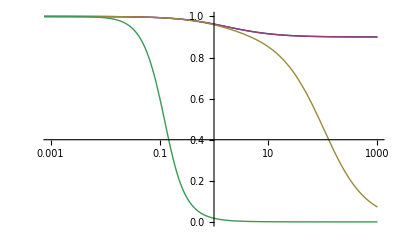

```mathematica
Print["For equation 7.23 : 
",eqn,"
We use values : ",sub0={h->0.5,Subscript[Ω, b]->1}   ,"
and we use a value for k_eq = ",NumericalValues[Subscript[k, eq]/.subkeq]/.sub0
];
tmpeqn=eqn/.Subscript[k, eq]->Subscript[k, eq]/sec2Mpc   (* Mpc units *);
tmpeqn=NumericalValues[tmpeqn/.subkeq/.subsec2Mpc/.subaeq]/.sub0;

y0=10^-10;y1=10^3;maxit=15;
Print["Eqn 7.23 with numerical values becomes : 
", tmpeqn    ];
e732[[2]]/Φ[0];
Clear[s]
For[it=0,it<maxit,it++,
tmp=tmpeqn/.k->.5 10^-it;
s[it]=NDSolve[{tmp,Φ[y0]==1,Φ'[y0]==0},Φ,{y,y0,y1}];
]
LogLinearPlot[Evaluate[{(e732[[2]])/Φ[0], Φ[y]/.s[10],Φ[y]/.s[2],Φ[y]/.s[0]}],{y,y0,y1},PlotRange->{{.001,1000},{.0,1}},AxesOrigin->{1,.4}]
```

We compare this transfer function computed at y=1000 with BBKS transfer function, Eqn .7 .70 for k=[,].  We find that the values are similar but differ significantly.  Eqn 7.70 is for small scale, k>>k_eq.

k→0.5(Mpc^-1) -->  {7.56653×10^-6}  --> 21.1192 --> 0.0398745

k→0.05(Mpc^-1) -->  {0.000757296}  --> 2.11192 --> 0.485588

k→0.005(Mpc^-1) -->  {0.0720113}  --> 0.211192 --> 0.954329

k→0.0005(Mpc^-1) -->  {0.828614}  --> 0.0211192 --> 0.996554

k→0.00005(Mpc^-1) -->  {0.899436}  --> 0.00211192 --> 0.999668

k→5.×10^-6(Mpc^-1) -->  {0.900192}  --> 0.000211192 --> 0.999967

k→5.×10^-7(Mpc^-1) -->  {0.900199}  --> 0.0000211192 --> 0.999997

k→5.×10^-8(Mpc^-1) -->  {0.900199}  --> 2.11192×10^-6 --> 1.

k→5.×10^-9(Mpc^-1) -->  {0.900199}  --> 2.11192×10^-7 --> 1.

k→5.×10^-10(Mpc^-1) -->  {0.900199}  --> 2.11192×10^-8 --> 1.

k→5.×10^-11(Mpc^-1) -->  {0.900199}  --> 2.11192×10^-9 --> 1.

k→5.×10^-12(Mpc^-1) -->  {0.900199}  --> 2.11192×10^-10 --> 0.999998

k→5.×10^-13(Mpc^-1) -->  {0.900199}  --> 2.11192×10^-11 --> 0.999985

k→5.×10^-14(Mpc^-1) -->  {0.900199}  --> 2.11192×10^-12 --> 0.99974

k→5.×10^-15(Mpc^-1) -->  {0.900199}  --> 2.11192×10^-13 --> 1.0022

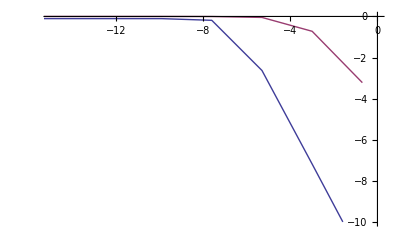

```mathematica
Tran[x_]:=Log[1+.171 x]/(.171 x)(1+.284 x + ( 1.18  x )^2 +(.399 x )^3 +(.490 x )^4 )^(-.25)
For[it=0,it<maxit,it++,
Print[
sk=k->(kk[it]=.5 10^-it),"(Mpc^-1) -->  ",
phi[it]=Φ[y1]/.s[it],"  --> ",
x=NumericalValues[ kk[it]/(Subscript[k, eq]/sec2Mpc)/.subkeq/.subsec2Mpc]/.sub0," --> ",
bbks[it]=Tran[x]
];
]

t=Table[{Log[kk[it]],Log[phi[it][[1]]]},{it,0,maxit-1,1}];
t2=Table[{Log[kk[it]],Log[bbks[it]]},{it,0,maxit-1,1}];
ListLinePlot[{t,t2},PlotRange->{{-maxit,0},{-10,0}}]
```

Set up for numerical solutions to Eqn.7.11-.15.  We construct general coordinate transformation routine,  fromη2y.

```mathematica
<<Dodelson`ChangeVariable`
Clear[y,η,neweqns]
CurrentEqns
elist=CurrentEqns//ReleaseHold;
neqn=Length[elist];
neweqns={};
For[i=1,i<=neqn,i++,
Print[
eqn=elist[[i]],"
",neweqn=ChangeDfDxDyVar[ChangeDfDxDyDoAll[eqn,η,y],η,y],"
*******************"];
neweqns=Append[neweqns,neweqn];
]
Print[ColumnForm[neweqns]]
```

{e711,e712,e713a,e714c,e715B}

k Θ_1(η)+Θ_0'(η)==-Φ'(η)
k Θ_1(y)+(Θ_0'(y))/(η'(y))==-(Φ'(y))/(η'(y))
*******************

Θ_1'(η)-1/3 k Θ_0(η)==-1/3 k Φ(η)
(Θ_1'(y))/(η'(y))-1/3 k Θ_0(y)==-1/3 k Φ(y)
*******************

δ'(η)-k vi(η)==-3 Φ'(η)
(δ'(y))/(η'(y))-k vi(y)==-(3 Φ'(y))/(η'(y))
*******************

k y(η) Φ(η)==y(η) vi'(η)+vi(η) y'(η)
k y Φ(y)==(vi(y))/(η'(y))+(y vi'(y))/(η'(y))
*******************

k^2 Φ(η) (y(η))^2+3 y'(η) Φ'(η) y(η)+3 Φ(η) (y'(η))^2==(3 H_0^2 (a_eq Ω_b y(η) δ(η) h^2+4 C_γ Θ_0(η)))/(2 h^2 a_eq^2)
k^2 Φ(y) y^2+(3 Φ'(y) y)/(η'(y))^2+(3 Φ(y))/(η'(y))^2==(3 H_0^2 (y a_eq Ω_b δ(y) h^2+4 C_γ Θ_0(y)))/(2 h^2 a_eq^2)
*******************

k Θ_1(y)+(Θ_0'(y))/(η'(y))==-(Φ'(y))/(η'(y))
(Θ_1'(y))/(η'(y))-1/3 k Θ_0(y)==-1/3 k Φ(y)
(δ'(y))/(η'(y))-k vi(y)==-(3 Φ'(y))/(η'(y))
k y Φ(y)==(vi(y))/(η'(y))+(y vi'(y))/(η'(y))
k^2 Φ(y) y^2+(3 Φ'(y) y)/(η'(y))^2+(3 Φ(y))/(η'(y))^2==(3 H_0^2 (y a_eq Ω_b δ(y) h^2+4 C_γ Θ_0(y)))/(2 h^2 a_eq^2)

Equations in terms of kk_eq=k/k_eq  --> 2 kk_eq Θ_1(y)+√2 √(y+1) Φ'(y)+√2 √(y+1) Θ_0'(y)==0
2 kk_eq Φ(y)-2 kk_eq Θ_0(y)+3 √2 √(y+1) Θ_1'(y)==0
2 kk_eq vi(y)-√2 √(y+1) δ'(y)-3 √2 √(y+1) Φ'(y)==0
√2 √(y+1) vi(y)-2 y kk_eq Φ(y)+√2 y √(y+1) vi'(y)==0
6 Φ'(y) y^2-3 δ(y) y+6 Φ'(y) y+(4 y^2 kk_eq^2+6 y+6) Φ(y)-12 Θ_0(y)==0

We set up for numerical solution using dependent variables : {Φ,Θ_0,δ,vi,Θ_1}
and ICs --> vi(0)==-3 Θ_1(0)
Θ_1(0)==-(k Φ(0))/(6 a H)
Θ_0(0)==(Φ(0))/2
δ(0)==3 Θ_0(0)

{Φ(y),Θ_0(y),δ(y),vi(y),Θ_1(y)}

We integrate these equations for different values of k/k_eq. First k=0.

{{Φ(0)→-0.0358162,Θ_0(0)→-0.0179081,δ(0)→-0.0537243,vi(0)→0.,Θ_1(0)→0.}}

Limits of integration y=:  0.0001 to 1000

The simplified k=0 set of equations is : Φ(y)+Θ_0(y)==-0.0537243
δ(y)+3 Φ(y)==-0.161173
2 ((y+1) (Φ(y)+y Φ'(y))-2 Θ_0(y))==y δ(y)
Φ(0)==2 Θ_0(0)
δ(0)==3 Θ_0(0)
Φ(0)+0.0358162==0

The integrated δ and Θ_0 approach yield rule: {Φ(y)→((-2. y-2.) Φ'(y) y-0.161173 y-0.214897)/(5. y+6.)}
We have the equations
{Φ(y)==((-2. y-2.) Φ'(y) y-0.161173 y-0.214897)/(5. y+6.)}
and the ICs :
{Φ(0.0001)+0.0358162==0}
The differential equation is rewritten : 
{0.161173 y+(5. y+6.) Φ(y)+(2. y^2+2. y) Φ'(y)+0.214897==0}

InterpolatingFunction::dmval: Input value TraditionalForm`{-9.21001} lies outside the range of data in the interpolating function. Extrapolation will be used.

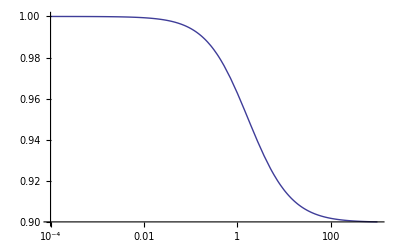

Let us try the to get Eqn.7.25 with these equations.

δ'(y)+3 Φ'(y)==0

(6 (y+1) (Φ(y)+y Φ'(y)))/(3 y+4)==δ(y)

(6 (Φ(y)+y Φ'(y)))/(3 y+4)-(18 (y+1) (Φ(y)+y Φ'(y)))/(3 y+4)^2+(6 (y+1) (2 Φ'(y)+y Φ''(y)))/(3 y+4)==δ'(y)

We are again at Eqn.7.25 : 2 Φ(y)+(21 y^2+54 y+32) Φ'(y)+2 y (3 y^2+7 y+4) Φ''(y)==0

```mathematica
Clear[y,η]
eqn1=neweqns/.η->Subscript[η, y];
eqn1=%/.subH0/.Subscript[k, eq]->k/Subscript[kk, eq]/.subaeq//PowerExpand;
eqnkk=(Collect[DeleteCommonFactors[#],{Φ[y],Subscript[Θ, 0][y],δ[y],vi[y],Subscript[Θ, 1][y]}] &)/@%;
Print["Equations in terms of kk_eq=k/k_eq  --> ",ColumnForm[eqnkk]];
eqnkk/.Subscript[kk, eq]->0//ColumnForm;
(*
eqnk0=Map[DeleteCommonFactors,eqnkk/.Subscript[kk, eq]->0];
Print["For the super-horizon case, k=0 we have --> ",ColumnForm[eqnk0],"
which show vi[y] decoupled from other parameters and  will lead to Eqn.732."
];
*)
Print["We set up for numerical solution using dependent variables : ",
vars={Φ,Subscript[Θ, 0],δ,vi,Subscript[Θ, 1]},"
and ICs --> ",
ColumnForm[CurrentICs//ReleaseHold]
]
ics=Join[CurrentICs//ReleaseHold,{Φ[0]==-Ψ[0]}];
ics=ReleaseHold[ics]/.k->Subscript[kk, eq] Subscript[k, eq]/.a->√(y+1)Subscript[k, eq]/(H √2)//Simplify;
ics=ics/.ic5;
%//ColumnForm;
varsy=Through[vars[y]]
s2=Solve[eqnkk[[1]],D[varsy[[2]],y]];
s3=Solve[eqnkk[[3]],D[varsy[[3]],y]];

eqnkk[[5]]=(Expand[Simplify[#/y]]&)/@eqnkk[[5]];
deqn=D[eqnkk,y];
de5=deqn[[5]];
de5/.s3[[1]]/.s2[[1]] //Simplify;

Print["We integrate these equations for different values of k/k_eq. First k=0."];
eqn2=eqnkk/.Subscript[kk, eq]->0;
eqn2=(DeleteCommonFactors[#]&)/@eqn2;
ics2=ics/.Subscript[kk, eq]->0;
subic=Solve[ics2,Through[vars[0]]]

ColumnForm[eqn2=eqn2//FullSimplify];
ColumnForm[eqnAll=Join[eqn2,ics2]];
eqnAllin=Pick[eqnAll,{1,0,1,0,1,  0,0,1,1,1},1];
Print["Limits of integration y=:  ",y0=0.0001," to ",y1=1000];(* k=0 special manipulation: There are 2 ways (1) substitute the integrated relationships of δ, etc. (2) substitute into differential of energy equation. *)
tmp=Integrate[eqnAllin[[1,1]],y];
tmpv=tmp/.y->0/.subic[[1]];
eqnAllin[[1]]=tmp==tmpv;
tmp=Integrate[eqnAllin[[2,1]],y];
tmpv=tmp/.y->0/.subic[[1]];
eqnAllin[[2]]=tmp==tmpv;
Print["The simplified k=0 set of equations is : ",
eqnAllin//ColumnForm
];
tmp=D[eqnAllin[[3]],y];
eqn3=Pick[eqnAllin,{1,1,1,0,0,0},1];
Print["The integrated δ and Θ_0 approach yield rule: ",
sPhi1=Solve[eqn3,Pick[varsy,{1,0,0,0,0},1],Pick[varsy,{0,1,1,0,0},1]][[1]]//Simplify,"
We have the equations
",Phi1=sPhi1/.Rule->Equal,"
and the ICs :
",ic=Pick[eqnAllin,{0,0,0,0,0,1},1]/.A_[0]->A[y0],"
The differential equation is rewritten : 
",
Phi1=Collect[Map[DeleteCommonFactors,Phi1],{Φ'[y],Φ[y]}]
];
eqnIn=Join[Phi1,ic];
varin=Pick[vars,{1,0,0,0,0},1];
s=NDSolve[eqnIn,varin,{y,y0,y1}];
LogLinearPlot[Evaluate[{ Φ[y]/-.035816193445799595/.s}],{y,y0,y1}]

Print["Let us try the to get Eqn.7.25 with these equations."];
e3=Pick[eqnAll,{0,0,1,0,0,  0,0,0,0,0},1][[1]]
e5=Pick[eqnAll,{0,0,0,0,1,  0,0,0,0,0},1][[1]];
e5=e5/.Subscript[Θ, 0][y]->δ[y]/3;
DeleteCommonFactors[e5]//Simplify;
e5=(#/(3y+4)&)/@%
tmp=D[e5,y]
tmp=Solve[{tmp,e3},{Φ[y]},{δ'[y]}][[1,1]]/.Rule->Equal;
Print["We are again at Eqn.7.25 : ",
e725=DeleteCommonFactors[tmp]//Simplify];
```

{{Φ→InterpolatingFunction[(0.0001 | 1000.),<>]}}

InterpolatingFunction::dmval: Input value TraditionalForm`{-9.21001} lies outside the range of data in the interpolating function. Extrapolation will be used.

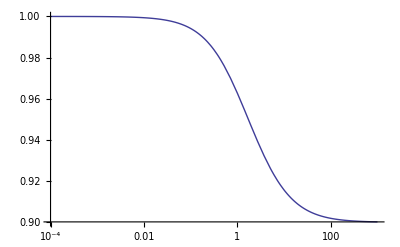

The above is the solution of the 2nd order equation for Φ.  These numerical solutions are consistent with Eqn.7.32.

```mathematica
s=NDSolve [ { e725,Φ'[y0]==0,Φ[y0]+0.035816193445799595==0},{Φ},{y,y0,y1}]
LogLinearPlot[Evaluate[{ Φ[y]/-.035816193445799595/.s}],{y,y0,y1}]
Print["The above is the solution of the 2nd order equation for Φ.  These numerical solutions are consistent with Eqn.7.32."]
```

Limits of integration y=:  0.0001 to 1000

The integration of the k ≠ 0 case gives :

InterpolatingFunction::dmval: Input value TraditionalForm`{-9.21001} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of TraditionalForm`InterpolatingFunction :: "dmval" will be suppressed during this calculation.

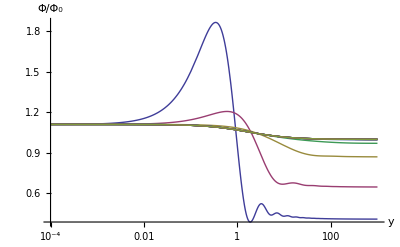

The transfer function is the ratio : T==(Φ(k,a_late))/(Φ_ls(k,a_late))
Where a_late ~ y=1000 and ls(largescale) corresponds to k=0.

Plot of these computed transfer function(red) to the BBKS transfer function(blue) is shown below and over the range of the plot they are very similar.

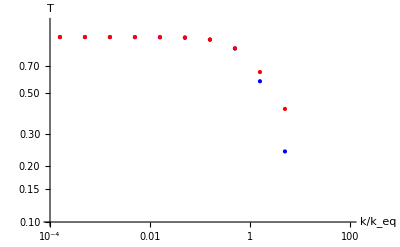

Since the solutions only depend upon k_eq == .073 Mpc^-1Ω_m h^2, the differences in the transition function between CDM and ΛCDM shift slightly the position of the curves.

```mathematica
Print["Limits of integration y=:  ",y0=0.0001," to ",y1=1000];
eqnkk;
%//ColumnForm;
icsIn=ics/.A_[0]->A[y0]/.y->y0;
 %//ColumnForm;
eqnIn=Join[eqnkk,icsIn];
%//ColumnForm;
varin=Pick[vars,{1,1,1,1,1},1];
Print["The integration of the k ≠ 0 case gives : "];


Clear[ss]
ss={};
ks={};
For[i=1,i<=16,i++,kfac=5(10^(-(i-1)/2));
eqns=eqnIn/.Subscript[kk, eq]->kfac;
List[i,",",kfac,",",eqns//ColumnForm];
s=NDSolve[eqns,varin,{y,y0,y1}][[1]];
AppendTo[ss,s];
AppendTo[ks,kfac];
];
(* k = 0 calculation *)
eqns=eqnIn/.Subscript[kk, eq]->0;
s=NDSolve[eqns,varin,{y,y0,y1}][[1]];
(*
AppendTo[ss,s];
AppendTo[ks,0]
*)
Phi0=Φ[y1]/.s;
LogLinearPlot[Evaluate[{ Φ[y]/Phi0/.ss}],{y,y0,y1},PlotRange->All
,AxesLabel->{"y","Φ/Φ_0"}
]
Print["The transfer function is the ratio : ",T==Φ[k,Subscript[a, late]]/(Subscript[Φ, ls][k,Subscript[a, late]]),"
Where a_late ~ y=1000 and ls(largescale) corresponds to k=0."]
transfer=Φ[y1]/Phi0/.ss;
tBBKS[x_]:=Log[1+0.171 x]/(0.171 x)(1+.284 x + (1.18 x)^2+(0.399 x )^3 + (.490 x)^4)^(-.25)
t2=Table[{y,tBBKS[y]},{y,ks}];
t1=Table[{ ks[[i]] ,transfer[[i]] },{i,1,Length[ks]}];
Print["Plot of these computed transfer function(red) to the BBKS transfer function(blue) is shown below and over the range of the plot they are very similar."]
Print[
ListLogLogPlot[{Tooltip[{t2},"BBKS"],Tooltip[{t1},"DifEqn"]},PlotRange->{{.0001,100},{.1,1.2}}
,PlotStyle->{{Blue,PointSize[Large]},{Red,PointSize[Medium]}}
,AxesLabel->{"k/k_eq","T"}
]
]
Print["Since the solutions only depend upon k_eq == .073 Mpc^-1Ω_m h^2, the differences in the transition function between CDM and ΛCDM shift slightly the position of the curves."]
```